Day5 - Nathan Yee

Initalization

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nathan/QEA-Homework/module2/day5

Data

```mathematica
barData=Import["bar.csv"];
svp=Import["svp.csv"];
stateData=Import["stateData.csv"];
```

Functions

```mathematica
Basic[data_]:={{"Mean",N@Mean[data]},{"Median",Median[data]},{"Variance",N@Variance[data]},{"Standard Deviation",N@StandardDeviation[data]}}
```

```mathematica
MyCorrelation[data1_,data2_]:=(Total[(data1-Mean[data1])*(data2-Mean[data2])]/(Length[data1]*StandardDeviation[data1]*StandardDeviation[data2]))
```

Question 1

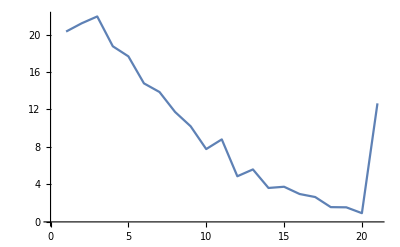

```mathematica
ListLinePlot[barData[[All,2]]]
```

Question 2

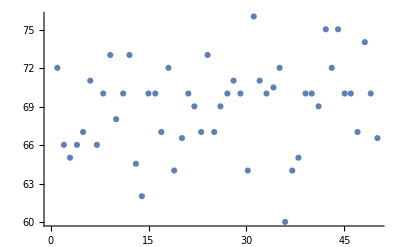

```mathematica
ListPlot[svp]
```

Question 3

Mean = 2

Standard Deviation = 1

Question 4

```mathematica
dataQuestion4={57,61,46,43,46,46,46,46,55}
```

{57,61,46,43,46,46,46,46,55}

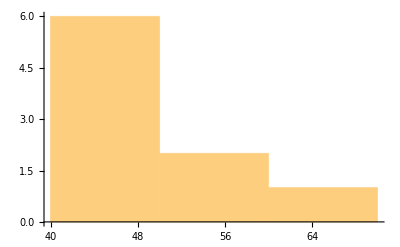

```mathematica
Histogram[dataQuestion4]
```

```mathematica
Grid[Basic[dataQuestion4], Frame->All]
```

Mean | 49.5556
Median | 46
Variance | 40.2778
Standard Deviation | 6.34648

Standard deviations can vary wildly with a small sample size

```mathematica
Question 5
```

```mathematica
dataQuestion5={63,66,71,65,70,66,67,65,67,74,64,75,68,67,70,73,66,70,72,62,68,70,62,69,66,70,70,68,69,70,71,65,64,71,64,78,69,70,65,66,72,64};
```

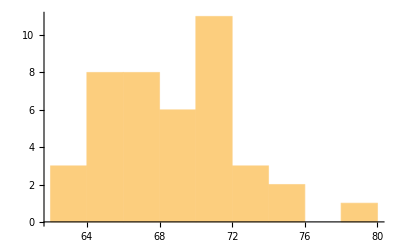

```mathematica
Histogram[dataQuestion5,10]
```

```mathematica
Grid[Basic[dataQuestion5],Frame->All]
```

Mean | 68.1429
Median | 68
Variance | 12.7596
Standard Deviation | 3.57206

The mean looks like it should be less than 70 and greater than 65.

The Standard Deviation looks like it should be in the range of 3 - 5

Question 7

```mathematica
Grid[Transpose@{{"Correlated: Doctors, University","Anticorrelated: Income, Poverty","Uncorrelated: Unemployed, Infant Mort"},{N@MyCorrelation[stateData[[2;;All,6]],stateData[[2;;All,8]]],
N@MyCorrelation[stateData[[2;;All,10]],stateData[[2;;All,2]]],
N@MyCorrelation[stateData[[2;;All,9]],stateData[[2;;All,3]]]}},Frame->All]
```

Correlated: Doctors, University | 0.678463
Anticorrelated: Income, Poverty | -0.825479
Uncorrelated: Unemployed, Infant Mort | -0.145022

Question 8

A. Plug them into mu function

B. I don’t understand question.  I’ll ask when I get the chance during checkoff or in class.

Question 9

Question 10

```mathematica
a=(24-22)/(300-60);
```

```mathematica
N@Solve[22==(a*60)+b,b][[1]][[1]]
```

b→21.5

Question 11

Same as question 10

Question 12

```mathematica
Clear[a,b]
```

```mathematica
A=({{60, 1}, {300, 1}});
x=({{a}, {b}});
B=({{22}, {24}});
```

```mathematica
Solve[A.x==B,{a,b}]
```

{{a→1/120,b→43/2}}

```mathematica
Inverse[A].B
```

{{1/120},{43/2}}

Question 13

```mathematica
t={53,54,58,66,69,70,71,73,81};
c={19,26,21,33,31,36,36,38,45};
```

```mathematica
x=Total[c];
y=Total[t];
x2=Total[c^2];
xy=Total[c*t];
n=Length[c]
```

9

Question 14

```mathematica
Clear[a,b]
```

```mathematica
solutions=N@Solve[a*x2+b*x==xy&&n*b+a*x==y,{a,b}]
```

{{a→1.06265,b→32.4606}}

```mathematica
{a,b}={a,b}/.solutions[[1]]
```

{1.06265,32.4606}

```mathematica
CricketTemp[x_]:=a*x+b
```

```mathematica
p1=Plot[CricketTemp[i],{i,15,50},PlotRange->{{0,Automatic},{0,Automatic}}];
p2=ListPlot[Transpose[Join[{c},{t}]]];
```

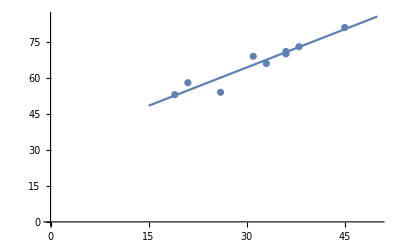

```mathematica
Show[p1,p2]
```

Question 15

```mathematica
Clear[a,b]
```

```mathematica
"(x | n
x2 | x).(a
b)=(y
xy)";
A=({{x, n}, {x2, x}});
u=({{a}, {b}});
B=({{y}, {xy}});
```

```mathematica
N@Inverse[A].B
```

{{1.06265},{32.4606}}